```mathematica
(*このファイルのコードでは有限要素法により拡散方程式を解いた結果の剛性行列から隣接行列を差癖する*)
```

## 1~9 の数字 (+インレット) の領域を作成する

```mathematica
inletPosition={{0,1.2},{0.3,2}} (*this gives the dimensions of the inlet*)
inlet=Rectangle@@inletPosition;
listRegion=ParallelTable[
t=Text[Style[char,Bold]];
Ω=RegionUnion[inlet,#]&@TransformedRegion[#,0.5*{(Indexed[#,1]+0),(Indexed[#,2]+0)}&]&@BoundaryDiscretizeGraphics[t,_Text,MaxCellMeasure->0.03,PlotRange->All],
{char,ToString/@Range@9}];
```

{{0,1.2},{0.3,2}}

#### 作成した領域の表示 （確認）

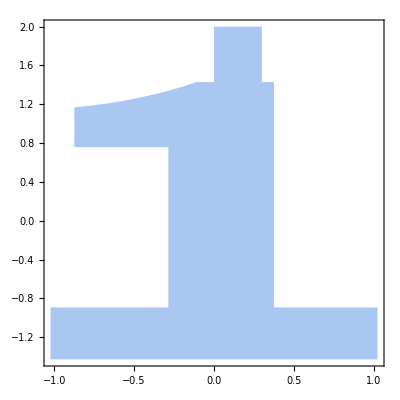
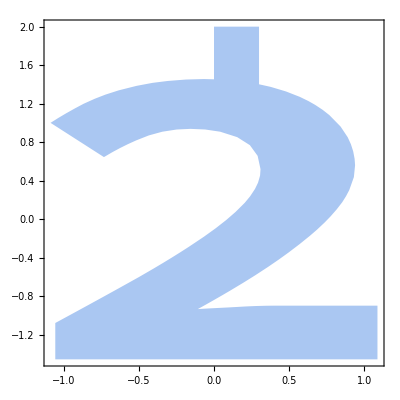
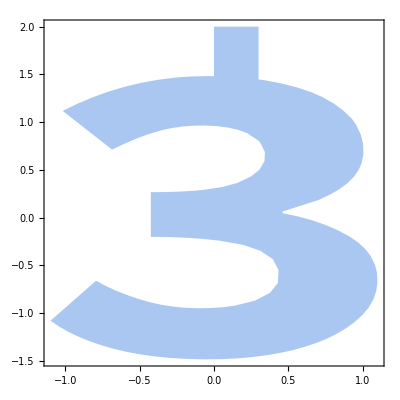
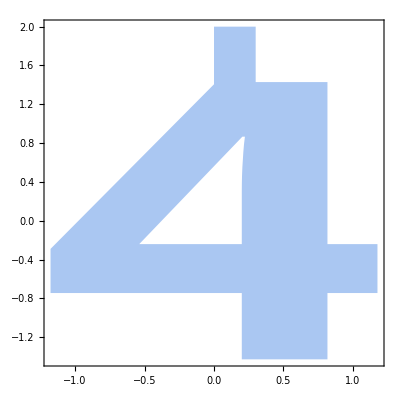
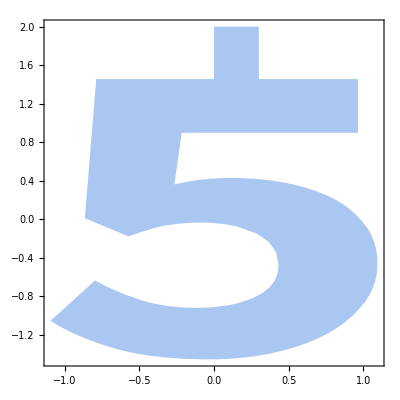
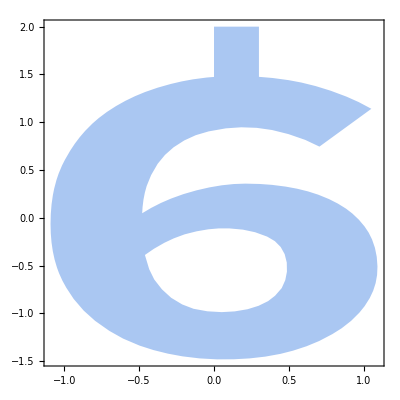
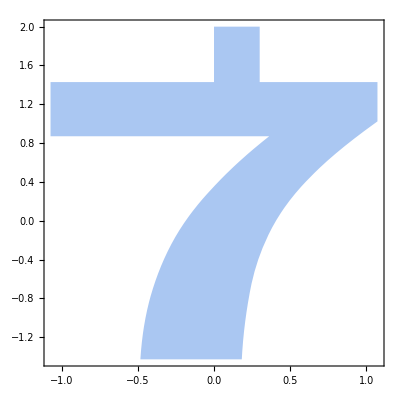
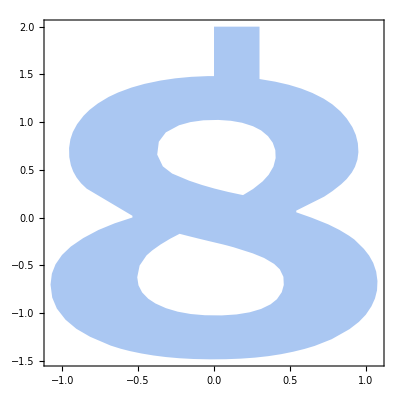

```mathematica
Region[#,AspectRatio->1,Frame->True]&@
RegionUnion[inlet,#]&/@listRegion
```

## 作成した全領域の隣接行列を一括で作成する 数字の1~9 から生成した領域にnBeads個の点をランダムに配置し，それぞれの数字に対してnSample個の隣接行列を作る． これらの隣接行列をデータセットとして隣接行列がどの数字から得られたものかを推定するのが今回の目的．

```mathematica
(*要素数はMaxCellMeasureを変えてもあまり変わらないので固定する*)

Needs["NDSolve`FEM`"]
SetDirectory[NotebookDirectory[]];

(*Fixed parameters*)
cellSize=0.01;
testRate=0.2;
t=20;
nBeads=100;
nSample=700;

adjMatTargets=ParallelTable[
Ω=listRegion[[i]];
maxcellsize=cellSize;

nr=ToElementMesh[#,MaxCellMeasure->maxcellsize]&@BoundaryDiscretizeRegion@Ω;

vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[2]}},"DampingCoefficients"->{{1}}};

initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

(*e-^tMを隣接行列とみなす場合は要素の頂点数と同じ数の種類のビーズを使うことを仮定している*)
(*次元が大きいと行列の指数関数を計算するのが大変なので用いたビーズの種類に次元を縮める*)
n=Length@stiffness;  (*要素数*)


(*今回はサンプルするたびにビーズの初期位置だけをランダムに変更し，メッシュの切り方やPDEの計算結果はサンプル間で同じものを用いる*)
ParallelTable[
(*最初にビーズを配置する節点のインデックスを重複のないように用いるビーズの数だけランダムに選ぶ*)
iInitialPoints=RandomSample[Range[n],nBeads];
(*i番目のビーズの領域に初期濃度を(1,要素数)のi番目だけが1の単位ベクトルとして表している
そのような単位ベクトルをビーズの種類数だけ集めて行列Vを形成している*)
V=Table[UnitVector[n,iInitialPoints[[iBead]]],{iBead,nBeads}];
(*剛性行列stiffnessは(要素数,要素数)と非常に大きいのでそのまま指数行列を計算するのは大変
そこでmathematicaの機能によりあらかじめVをかけることで次元を減らし計算量の低減している*)
R=Chop@MatrixExp[t*stiffness,#]&/@V;
(*隣接行列を計算した後，(1,ビーズ数^2)に整形し，最後にターゲットの番号(1~9)を追加する*)
M=R.Transpose[R];
(*隣接行列の1/n(定常態の時隣接行列の要素)より小さい要素を0に置き換える*)
adjMat=M/.x_/;x<1.0/n->0;
Append[Flatten[adjMat],i]
,nSample],
{i,Range@Length@listRegion}
];
adjMatTargets=Flatten[adjMatTargets,1];
(*Export adjacency matrices*)
Export[
(*"adj_mat/shape:"<>ToString[i]<>"beads:"<>Tostring<>"_t="<>ToString[t]<>".mtx",*)
(*ToString/@{"adjMatTargets","_beads=",nBeads,"_time=",t,".mtx"}//StringJoin,*)
"adjMatTargets.mtx",
SparseArray@adjMatTargets
];
```

ParallelTable::subpar: -- Message text not found --

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: -- Message text not found --

## 1 種類の図形によるテスト

{40,1090}

{40,1090}

{1090,40}

{{0.215094,0.,-1.16162×10^-10,0.,0.,-6.4553×10^-6,0.,0.00778231,0.123934,-5.58718×10^-17,0.,0.,3.33994×10^-6,0.,0.,0.,0.,-1.57622×10^-8,0.,0.,0.,0.,0.,0.,0.,-1.29178×10^-12,0.0000180511,0.,0.0000519346,2.67488×10^-17,0.,1.52512×10^-19,0.,-4.97332×10^-11,0.,0.,1.52398×10^-6,1.7806×10^-17,0.,-1.49167×10^-12},{0.,0.21868,0.,1.77631×10^-8,0.000332143,0.,-7.3785×10^-18,0.,0.,1.65149×10^-15,1.08216×10^-15,1.50644×10^-10,0.,-6.87732×10^-12,1.44418×10^-6,-1.18489×10^-9,-5.83824×10^-9,0.,-1.23395×10^-11,-3.22781×10^-17,1.70116×10^-9,-2.95424×10^-7,2.09428×10^-6,0.00231619,1.02658×10^-9,2.03181×10^-18,0.,-2.64624×10^-7,0.,2.11553×10^-16,-0.00155835,9.50846×10^-14,1.81948×10^-9,0.,-2.53932×10^-7,2.19897×10^-9,0.,1.66988×10^-12,2.91617×10^-15,0.},{-1.16162×10^-10,0.,0.307435,1.20786×10^-19,0.,-5.58681×10^-10,0.,2.21408×10^-10,-6.16041×10^-11,-3.27997×10^-11,0.,0.,-1.37105×10^-6,0.,0.,0.,0.,0.0000253787,0.,0.,0.,0.,0.,0.,0.,-1.01883×10^-7,-8.84789×10^-6,-7.54635×10^-19,-7.28781×10^-10,4.9875×10^-11,0.,-4.75173×10^-12,0.,-4.87929×10^-8,0.,0.,-3.35445×10^-10,2.52971×10^-11,-3.69975×10^-15,0.000251783},{0.,1.77631×10^-8,1.20786×10^-19,0.310064,-3.47355×10^-12,0.,0.,0.,0.,1.62136×10^-9,0.,0.020763,3.76825×10^-20,8.46546×10^-17,2.27761×10^-12,-4.68349×10^-16,-7.45804×10^-8,5.24375×10^-18,0.,0.,0.133602,-3.25253×10^-16,-2.32436×10^-14,-2.02716×10^-10,-3.5021×10^-14,2.98796×10^-12,7.48419×10^-20,0.0000507426,0.,1.18041×10^-10,1.46755×10^-10,1.31865×10^-8,-4.24908×10^-18,0.,2.89931×10^-15,1.32047×10^-12,0.,2.26074×10^-7,1.13474×10^-9,0.},{0.,0.000332143,0.,-3.47355×10^-12,0.205286,0.,-6.77745×10^-18,0.,0.,0.,1.01894×10^-15,-1.57392×10^-14,0.,-7.11126×10^-12,5.57888×10^-6,-3.61595×10^-9,-8.98367×10^-12,0.,-3.48226×10^-14,-2.87881×10^-20,-2.40292×10^-13,-7.04458×10^-10,0.0173642,0.0153314,4.57851×10^-10,0.,0.,4.20967×10^-11,0.,0.,7.48945×10^-6,-4.30801×10^-18,7.84322×10^-12,0.,-3.10254×10^-9,5.49768×10^-10,0.,-1.26698×10^-16,0.,0.},{-6.4553×10^-6,0.,-5.58681×10^-10,0.,0.,0.211883,0.,-0.00175314,-0.0000651049,1.43506×10^-14,0.,0.,0.000416508,0.,0.,0.,0.,1.79152×10^-6,0.,0.,0.,0.,0.,0.,0.,1.88894×10^-11,4.68571×10^-6,0.,0.0388341,4.45927×10^-14,0.,-2.5182×10^-16,0.,5.63753×10^-13,0.,0.,0.0928942,-3.08434×10^-15,2.09213×10^-19,-6.87258×10^-13},{0.,-7.3785×10^-18,0.,0.,-6.77745×10^-18,0.,0.535065,0.,0.,0.,-0.0147968,0.,0.,-7.48828×10^-8,-4.54249×10^-14,3.12925×10^-16,-1.70526×10^-20,0.,0.,0.,0.,0.,0.,1.66232×10^-15,1.2819×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-2.58355×10^-11,0.,0.,0.,0.},{0.00778231,0.,2.21408×10^-10,0.,0.,-0.00175314,0.,0.319531,0.0437994,7.61401×10^-16,0.,0.,0.0000328942,0.,0.,0.,0.,-1.28458×10^-7,0.,0.,0.,0.,0.,0.,0.,1.07262×10^-11,-0.0000253574,0.,0.0240575,1.98352×10^-15,0.,-8.0158×10^-18,0.,6.94507×10^-11,0.,0.,-0.000323903,-2.2231×10^-16,0.,2.42659×10^-12},{0.123934,0.,-6.16041×10^-11,0.,0.,-0.0000651049,0.,0.0437994,0.208504,-1.93829×10^-17,0.,0.,2.0541×10^-6,0.,0.,0.,0.,-9.02044×10^-9,0.,0.,0.,0.,0.,0.,0.,-5.47896×10^-13,8.78552×10^-6,0.,0.00103675,7.52385×10^-18,0.,-2.67061×10^-20,0.,-2.32329×10^-11,0.,0.,6.17449×10^-6,5.20491×10^-18,0.,-7.24945×10^-13},{-5.58718×10^-17,1.65149×10^-15,-3.27997×10^-11,1.62136×10^-9,0.,1.43506×10^-14,0.,7.61401×10^-16,-1.93829×10^-17,0.217288,0.,2.03031×10^-12,-4.26639×10^-11,0.,0.,0.,7.9619×10^-16,-3.82777×10^-9,0.,0.,1.51536×10^-10,0.,0.,-6.71156×10^-18,0.,0.000252174,-3.88544×10^-11,-4.21972×10^-9,-2.56824×10^-15,-0.0012018,5.75379×10^-18,0.0221197,0.,-3.18877×10^-16,0.,0.,4.25203×10^-15,0.0217272,1.14939×10^-6,-6.43839×10^-16},{0.,1.08216×10^-15,0.,0.,1.01894×10^-15,0.,-0.0147968,0.,0.,0.,0.535681,0.,0.,0.000040892,2.64699×10^-12,-2.41806×10^-14,-2.80394×10^-18,0.,0.,0.,0.,0.,-5.56036×10^-18,-1.60271×10^-13,-7.92826×10^-8,0.,0.,0.,0.,0.,9.81369×10^-19,0.,0.,0.,0.,3.3802×10^-9,0.,0.,0.,0.},{0.,1.50644×10^-10,0.,0.020763,-1.57392×10^-14,0.,0.,0.,0.,2.03031×10^-12,0.,0.434006,0.,1.45791×10^-19,9.25414×10^-15,-7.57802×10^-19,-4.505×10^-8,0.,0.,0.,0.0174276,-4.58096×10^-19,-7.51701×10^-17,-1.31106×10^-12,-8.53241×10^-17,2.61878×10^-15,0.,2.66576×10^-7,0.,1.98027×10^-13,9.97296×10^-13,5.32795×10^-11,0.,0.,8.83671×10^-18,4.73598×10^-15,0.,1.07751×10^-9,3.36072×10^-12,0.},{3.33994×10^-6,0.,-1.37105×10^-6,3.76825×10^-20,0.,0.000416508,0.,0.0000328942,2.0541×10^-6,-4.26639×10^-11,0.,0.,0.214895,0.,0.,0.,0.,0.00480585,0.,0.,0.,0.,0.,0.,0.,-3.10611×10^-7,0.0137697,-2.35429×10^-19,0.000321301,-8.71678×10^-11,0.,1.20369×10^-12,0.,-4.32351×10^-9,0.,0.,-0.0000224582,1.34601×10^-11,-1.84696×10^-15,8.58436×10^-9},{0.,-6.87732×10^-12,0.,8.46546×10^-17,-7.11126×10^-12,0.,-7.48828×10^-8,0.,0.,0.,0.000040892,1.45791×10^-19,0.,0.214321,1.90398×10^-9,2.01039×10^-10,6.19892×10^-14,0.,0.,0.,2.34849×10^-18,0.,5.01064×10^-14,7.17504×10^-10,0.000237379,0.,0.,-3.75451×10^-16,0.,0.,-1.05079×10^-14,0.,0.,0.,2.55988×10^-19,1.96456×10^-6,0.,0.,0.,0.},{0.,1.44418×10^-6,0.,2.27761×10^-12,5.57888×10^-6,0.,-4.54249×10^-14,0.,0.,0.,2.64699×10^-12,9.25414×10^-15,0.,1.90398×10^-9,0.198594,0.0020736,2.92038×10^-11,0.,-1.63899×10^-17,0.,1.3451×10^-13,-1.42969×10^-14,4.79252×10^-8,-0.0000254248,2.84295×10^-7,0.,0.,-1.51807×10^-11,0.,0.,5.55428×10^-9,2.32224×10^-18,1.24899×10^-15,0.,-9.12783×10^-13,2.17401×10^-8,0.,7.14542×10^-17,0.,0.},{0.,-1.18489×10^-9,0.,-4.68349×10^-16,-3.61595×10^-9,0.,3.12925×10^-16,0.,0.,0.,-2.41806×10^-14,-7.57802×10^-19,0.,2.01039×10^-10,0.0020736,0.434005,-2.77685×10^-15,0.,0.,0.,-1.31578×10^-17,1.22287×10^-17,-2.75582×10^-11,2.09763×10^-7,-8.13078×10^-10,0.,0.,2.97574×10^-15,0.,0.,-2.85107×10^-12,0.,-2.66362×10^-19,0.,3.05761×10^-16,-3.15901×10^-10,0.,0.,0.,0.},{0.,-5.83824×10^-9,0.,-7.45804×10^-8,-8.98367×10^-12,0.,-1.70526×10^-20,0.,0.,7.9619×10^-16,-2.80394×10^-18,-4.505×10^-8,0.,6.19892×10^-14,2.92038×10^-11,-2.77685×10^-15,0.443648,0.,0.,0.,-1.01898×10^-8,-2.44185×10^-17,-4.08811×10^-14,1.07722×10^-9,2.57748×10^-10,5.45492×10^-19,0.,-3.02742×10^-8,0.,7.13261×10^-17,-9.08813×10^-12,2.72873×10^-14,-3.21458×10^-20,0.,-2.35008×10^-16,-1.66789×10^-8,0.,6.43888×10^-13,1.39643×10^-15,0.},{-1.57622×10^-8,0.,0.0000253787,5.24375×10^-18,0.,1.79152×10^-6,0.,-1.28458×10^-7,-9.02044×10^-9,-3.82777×10^-9,0.,0.,0.00480585,0.,0.,0.,0.,0.216743,0.,0.,-4.3066×10^-20,0.,0.,0.,0.,-1.20798×10^-6,-0.000604791,-3.28778×10^-17,6.5673×10^-7,-1.35936×10^-8,0.,2.09241×10^-10,0.,-6.29768×10^-9,0.,0.,1.13721×10^-6,1.3316×10^-9,-2.93137×10^-13,1.56457×10^-8},{0.,-1.23395×10^-11,0.,0.,-3.48226×10^-14,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.63899×10^-17,0.,0.,0.,0.316239,-3.61027×10^-6,0.,8.8409×10^-9,-1.11009×10^-14,1.31296×10^-13,0.,0.,0.,5.01759×10^-19,0.,0.,-3.09323×10^-9,0.,0.0000733911,0.,0.0000468094,0.,0.,0.,0.,0.},{0.,-3.22781×10^-17,0.,0.,-2.87881×10^-20,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-3.61027×10^-6,0.415888,0.,-2.48551×10^-13,0.,5.97112×10^-20,0.,0.,0.,0.,0.,0.,2.92777×10^-14,0.,1.2626×10^-8,0.,4.15628×10^-10,0.,0.,0.,0.,0.},{0.,1.70116×10^-9,0.,0.133602,-2.40292×10^-13,0.,0.,0.,0.,1.51536×10^-10,0.,0.0174276,0.,2.34849×10^-18,1.3451×10^-13,-1.31578×10^-17,-1.01898×10^-8,-4.3066×10^-20,0.,0.,0.209541,-3.16988×10^-18,-1.21891×10^-15,-1.68833×10^-11,-1.43416×10^-15,1.58721×10^-13,0.,0.0000105735,0.,6.85199×10^-12,1.17575×10^-11,-1.23101×10^-9,1.23852×10^-20,0.,1.27733×10^-16,7.7103×10^-14,0.,-4.80965×10^-9,3.94656×10^-11,0.},{0.,-2.95424×10^-7,0.,-3.25253×10^-16,-7.04458×10^-10,0.,0.,0.,0.,0.,0.,-4.58096×10^-19,0.,0.,-1.42969×10^-14,1.22287×10^-17,-2.44185×10^-17,0.,8.8409×10^-9,-2.48551×10^-13,-3.16988×10^-18,0.220639,-2.38382×10^-11,4.39693×10^-10,5.49745×10^-18,0.,0.,-6.37357×10^-14,0.,0.,0.000264524,0.,3.28021×10^-6,0.,2.03548×10^-6,1.19285×10^-17,0.,0.,0.,0.},{0.,2.09428×10^-6,0.,-2.32436×10^-14,0.0173642,0.,0.,0.,0.,0.,-5.56036×10^-18,-7.51701×10^-17,0.,5.01064×10^-14,4.79252×10^-8,-2.75582×10^-11,-4.08811×10^-14,0.,-1.11009×10^-14,0.,-1.21891×10^-15,-2.38382×10^-11,0.209553,0.000784404,1.799×10^-12,0.,0.,3.11361×10^-13,0.,0.,7.00056×10^-8,0.,4.77276×10^-13,0.,-3.31741×10^-10,2.80931×10^-12,0.,-4.61745×10^-19,0.,0.},{0.,0.00231619,0.,-2.02716×10^-10,0.0153314,0.,1.66232×10^-15,0.,0.,-6.71156×10^-18,-1.60271×10^-13,-1.31106×10^-12,0.,7.17504×10^-10,-0.0000254248,2.09763×10^-7,1.07722×10^-9,0.,1.31296×10^-13,5.97112×10^-20,-1.68833×10^-11,4.39693×10^-10,0.000784404,0.203885,-3.68502×10^-8,0.,0.,1.33139×10^-9,0.,-9.30884×10^-19,-5.88017×10^-6,-6.28438×10^-16,-9.06451×10^-12,0.,2.41661×10^-9,-4.94594×10^-8,0.,-1.30897×10^-14,-1.32947×10^-17,0.},{0.,1.02658×10^-9,0.,-3.5021×10^-14,4.57851×10^-10,0.,1.2819×10^-9,0.,0.,0.,-7.92826×10^-8,-8.53241×10^-17,0.,0.000237379,2.84295×10^-7,-8.13078×10^-10,2.57748×10^-10,0.,0.,0.,-1.43416×10^-15,5.49745×10^-18,1.799×10^-12,-3.68502×10^-8,0.195538,0.,0.,1.49563×10^-13,0.,0.,1.38085×10^-12,0.,0.,0.,5.09527×10^-18,0.0229086,0.,-2.87796×10^-19,0.,0.},{-1.29178×10^-12,2.03181×10^-18,-1.01883×10^-7,2.98796×10^-12,0.,1.88894×10^-11,0.,1.07262×10^-11,-5.47896×10^-13,0.000252174,0.,2.61878×10^-15,-3.10611×10^-7,0.,0.,0.,5.45492×10^-19,-1.20798×10^-6,0.,0.,1.58721×10^-13,0.,0.,0.,0.,0.20883,-3.16394×10^-7,-1.98817×10^-11,-3.58774×10^-11,0.000155788,0.,0.0000133019,0.,-1.24133×10^-11,0.,0.,-7.70825×10^-12,0.000037169,-3.98066×10^-8,-1.72938×10^-11},{0.0000180511,0.,-8.84789×10^-6,7.48419×10^-20,0.,4.68571×10^-6,0.,-0.0000253574,8.78552×10^-6,-3.88544×10^-11,0.,0.,0.0137697,0.,0.,0.,0.,-0.000604791,0.,0.,0.,0.,0.,0.,0.,-3.16394×10^-7,0.295332,-4.67589×10^-19,0.0000804,-1.61217×10^-11,0.,1.45798×10^-12,0.,-3.26389×10^-7,0.,0.,0.0000117432,1.5164×10^-11,-2.87729×10^-15,9.2982×10^-8},{0.,-2.64624×10^-7,-7.54635×10^-19,0.0000507426,4.20967×10^-11,0.,0.,0.,0.,-4.21972×10^-9,0.,2.66576×10^-7,-2.35429×10^-19,-3.75451×10^-16,-1.51807×10^-11,2.97574×10^-15,-3.02742×10^-8,-3.28778×10^-17,5.01759×10^-19,0.,0.0000105735,-6.37357×10^-14,3.11361×10^-13,1.33139×10^-9,1.49563×10^-13,-1.98817×10^-11,-4.67589×10^-19,0.20371,0.,-7.07901×10^-10,5.31518×10^-9,-1.90985×10^-7,-3.23309×10^-16,0.,7.79739×10^-14,-4.81012×10^-12,0.,-1.58019×10^-6,-5.83369×10^-9,0.},{0.0000519346,0.,-7.28781×10^-10,0.,0.,0.0388341,0.,0.0240575,0.00103675,-2.56824×10^-15,0.,0.,0.000321301,0.,0.,0.,0.,6.5673×10^-7,0.,0.,0.,0.,0.,0.,0.,-3.58774×10^-11,0.0000804,0.,0.211431,-7.04458×10^-15,0.,2.62046×10^-17,0.,-2.27493×10^-10,0.,0.,0.00643752,7.63288×10^-16,0.,-6.83782×10^-12},{2.67488×10^-17,2.11553×10^-16,4.9875×10^-11,1.18041×10^-10,0.,4.45927×10^-14,0.,1.98352×10^-15,7.52385×10^-18,-0.0012018,0.,1.98027×10^-13,-8.71678×10^-11,0.,0.,0.,7.13261×10^-17,-1.35936×10^-8,0.,0.,6.85199×10^-12,0.,0.,-9.30884×10^-19,0.,0.000155788,-1.61217×10^-11,-7.07901×10^-10,-7.04458×10^-15,0.299243,8.62224×10^-19,0.0000474507,0.,2.07766×10^-16,0.,0.,1.43221×10^-14,0.000562699,0.0000142751,-4.29003×10^-16},{0.,-0.00155835,0.,1.46755×10^-10,7.48945×10^-6,0.,0.,0.,0.,5.75379×10^-18,9.81369×10^-19,9.97296×10^-13,0.,-1.05079×10^-14,5.55428×10^-9,-2.85107×10^-12,-9.08813×10^-12,0.,-3.09323×10^-9,2.92777×10^-14,1.17575×10^-11,0.000264524,7.00056×10^-8,-5.88017×10^-6,1.38085×10^-12,0.,0.,5.31518×10^-9,0.,8.62224×10^-19,0.314835,5.9824×10^-16,-3.03856×10^-7,0.,-9.80899×10^-6,3.07841×10^-12,0.,1.15246×10^-14,1.31161×10^-17,0.},{1.52512×10^-19,9.50846×10^-14,-4.75173×10^-12,1.31865×10^-8,-4.30801×10^-18,-2.5182×10^-16,0.,-8.0158×10^-18,-2.67061×10^-20,0.0221197,0.,5.32795×10^-11,1.20369×10^-12,0.,2.32224×10^-18,0.,2.72873×10^-14,2.09241×10^-10,0.,0.,-1.23101×10^-9,0.,0.,-6.28438×10^-16,0.,0.0000133019,1.45798×10^-12,-1.90985×10^-7,2.62046×10^-17,0.0000474507,5.9824×10^-16,0.198041,0.,-1.02433×10^-17,0.,6.57439×10^-19,-4.69927×10^-17,0.00332736,5.12338×10^-7,6.05862×10^-17},{0.,1.81948×10^-9,0.,-4.24908×10^-18,7.84322×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.24899×10^-15,-2.66362×10^-19,-3.21458×10^-20,0.,0.0000733911,1.2626×10^-8,1.23852×10^-20,3.28021×10^-6,4.77276×10^-13,-9.06451×10^-12,0.,0.,0.,-3.23309×10^-16,0.,0.,-3.03856×10^-7,0.,0.216679,0.,-0.00170639,1.39375×10^-20,0.,0.,0.,0.},{-4.97332×10^-11,0.,-4.87929×10^-8,0.,0.,5.63753×10^-13,0.,6.94507×10^-11,-2.32329×10^-11,-3.18877×10^-16,0.,0.,-4.32351×10^-9,0.,0.,0.,0.,-6.29768×10^-9,0.,0.,0.,0.,0.,0.,0.,-1.24133×10^-11,-3.26389×10^-7,0.,-2.27493×10^-10,2.07766×10^-16,0.,-1.02433×10^-17,0.,0.508441,0.,0.,-3.58955×10^-12,3.20459×10^-16,0.,-0.0000170261},{0.,-2.53932×10^-7,0.,2.89931×10^-15,-3.10254×10^-9,0.,0.,0.,0.,0.,0.,8.83671×10^-18,0.,2.55988×10^-19,-9.12783×10^-13,3.05761×10^-16,-2.35008×10^-16,0.,0.0000468094,4.15628×10^-10,1.27733×10^-16,2.03548×10^-6,-3.31741×10^-10,2.41661×10^-9,5.09527×10^-18,0.,0.,7.79739×10^-14,0.,0.,-9.80899×10^-6,0.,-0.00170639,0.,0.297235,3.87987×10^-17,0.,5.95583×10^-20,0.,0.},{0.,2.19897×10^-9,0.,1.32047×10^-12,5.49768×10^-10,0.,-2.58355×10^-11,0.,0.,0.,3.3802×10^-9,4.73598×10^-15,0.,1.96456×10^-6,2.17401×10^-8,-3.15901×10^-10,-1.66789×10^-8,0.,0.,0.,7.7103×10^-14,1.19285×10^-17,2.80931×10^-12,-4.94594×10^-8,0.0229086,0.,0.,-4.81012×10^-12,0.,0.,3.07841×10^-12,6.57439×10^-19,1.39375×10^-20,0.,3.87987×10^-17,0.434006,0.,2.00645×10^-17,0.,0.},{1.52398×10^-6,0.,-3.35445×10^-10,0.,0.,0.0928942,0.,-0.000323903,6.17449×10^-6,4.25203×10^-15,0.,0.,-0.0000224582,0.,0.,0.,0.,1.13721×10^-6,0.,0.,0.,0.,0.,0.,0.,-7.70825×10^-12,0.0000117432,0.,0.00643752,1.43221×10^-14,0.,-4.69927×10^-17,0.,-3.58955×10^-12,0.,0.,0.220195,-8.3043×10^-16,0.,-5.44602×10^-13},{1.7806×10^-17,1.66988×10^-12,2.52971×10^-11,2.26074×10^-7,-1.26698×10^-16,-3.08434×10^-15,0.,-2.2231×10^-16,5.20491×10^-18,0.0217272,0.,1.07751×10^-9,1.34601×10^-11,0.,7.14542×10^-17,0.,6.43888×10^-13,1.3316×10^-9,0.,0.,-4.80965×10^-9,0.,-4.61745×10^-19,-1.30897×10^-14,-2.87796×10^-19,0.000037169,1.5164×10^-11,-1.58019×10^-6,7.63288×10^-16,0.000562699,1.15246×10^-14,0.00332736,0.,3.20459×10^-16,5.95583×10^-20,2.00645×10^-17,-8.3043×10^-16,0.325052,-0.000523872,-7.60421×10^-17},{0.,2.91617×10^-15,-3.69975×10^-15,1.13474×10^-9,0.,2.09213×10^-19,0.,0.,0.,1.14939×10^-6,0.,3.36072×10^-12,-1.84696×10^-15,0.,0.,0.,1.39643×10^-15,-2.93137×10^-13,0.,0.,3.94656×10^-11,0.,0.,-1.32947×10^-17,0.,-3.98066×10^-8,-2.87729×10^-15,-5.83369×10^-9,0.,0.0000142751,1.31161×10^-17,5.12338×10^-7,0.,0.,0.,0.,0.,-0.000523872,0.19532,0.},{-1.49167×10^-12,0.,0.000251783,0.,0.,-6.87258×10^-13,0.,2.42659×10^-12,-7.24945×10^-13,-6.43839×10^-16,0.,0.,8.58436×10^-9,0.,0.,0.,0.,1.56457×10^-8,0.,0.,0.,0.,0.,0.,0.,-1.72938×10^-11,9.2982×10^-8,0.,-6.83782×10^-12,-4.29003×10^-16,0.,6.05862×10^-17,0.,-0.0000170261,0.,0.,-5.44602×10^-13,-7.60421×10^-17,0.,0.202782}}

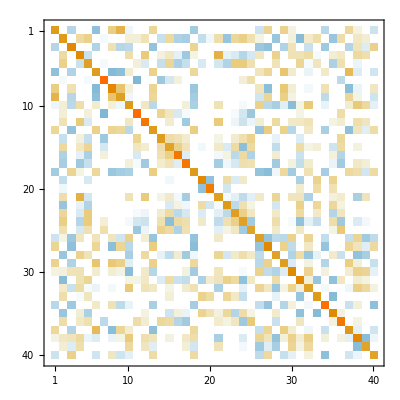

{1090,1090}

```mathematica
Needs["NDSolve`FEM`"]
SetDirectory[NotebookDirectory[]];

Ω=listRegion[[1]];
maxcellsize=.4;
(*ϵ=0*0.001;
τ=0.1;*)
nr=ToElementMesh[#,MaxCellMeasure->0.1]&@BoundaryDiscretizeRegion[Ω];

vd=NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y,z}}];
sd=NDSolve`SolutionData[{"Space"->nr}];

coefficients={"DiffusionCoefficients"->{{IdentityMatrix[3]}},"DampingCoefficients"->{{1}}};
initCoeffs=InitializePDECoefficients[vd,sd,coefficients];
methodData=InitializePDEMethodData[vd,sd];

(*Assembly of matrices*)
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];

n=Length@stiffness;
V=Table[UnitVector[n,RandomInteger[{1,n}]],{40}];
Dimensions@V
R=Chop@MatrixExp[.2*stiffness,#]&/@V;
Dimensions@R
Dimensions@Transpose@R
M=R.Transpose[R]
MatrixPlot@M
am=M/.x_/;x<0->0;
Export["stiffTest.mtx",SparseArray[am]];
Dimensions@stiffness
```

## その他の確認？

```mathematica
n=Length@stiffness;
V=Table[UnitVector[n,RandomInteger[{1,n}]],{40}];
Dimensions@V
R=Chop@MatrixExp[.2*stiffness,#]&/@V;
Dimensions@R
Dimensions@Transpose@R
M=R.Transpose[R]
MatrixPlot@M
```